```mathematica
NMAX=21; 
SetDirectory[NotebookDirectory[]];
```

## Make basis for harmonic polynomials "Run Section"

```mathematica
PrependTo[$Path,FileNameJoin[{$HomeDirectory,"Documents","Doktorarbeit","linuxfiles","Mathematica","SmatrixScripts"}]];
SetDirectory[NotebookDirectory[]];
Get["./Ypolynom_unrotated.mx"]
Get["./NormFactor_unrotated.mx"];
```

```mathematica
Ypolynom[[6]]
```

{5 x1^4 y1-10 x1^2 y1^3+y1^5,x1^3 y1 z1-x1 y1^3 z1,-3 x1^4 y1-2 x1^2 y1^3+y1^5+24 x1^2 y1 z1^2-8 y1^3 z1^2,-x1^3 y1 z1-x1 y1^3 z1+2 x1 y1 z1^3,x1^4 y1+2 x1^2 y1^3+y1^5-12 x1^2 y1 z1^2-12 y1^3 z1^2+8 y1 z1^4,15 x1^4 z1+30 x1^2 y1^2 z1+15 y1^4 z1-40 x1^2 z1^3-40 y1^2 z1^3+8 z1^5,-x1^5-2 x1^3 y1^2-x1 y1^4+12 x1^3 z1^2+12 x1 y1^2 z1^2-8 x1 z1^4,-x1^4 z1+y1^4 z1+2 x1^2 z1^3-2 y1^2 z1^3,x1^5-2 x1^3 y1^2-3 x1 y1^4-8 x1^3 z1^2+24 x1 y1^2 z1^2,x1^4 z1-6 x1^2 y1^2 z1+y1^4 z1,-x1^5+10 x1^3 y1^2-5 x1 y1^4}

```mathematica
NormFactor[[6]]
```

{1/(8 √30),1/(2 √3),1/(24 √6),1/6,1/(24 √7),1/(24 √105),1/(24 √7),1/12,1/(24 √6),1/(8 √3),1/(8 √30)}

## Spherical+Radial Definitions "Run Section"

```mathematica
couple[nA_,nB_,nResult_]:=If[EvenQ[nA+nB-nResult]&&(nA+nB-nResult≥0)&&(nA+nB-nResult≤2Min[nA,nB]),1,0]
```

```mathematica
p[x_,a_,n_]:=Sum[(-1)^p Gamma[n+a+3/2]/Gamma[n+p+3/2] Binomial[a,p] x^p,{p,0,a}]
```

```mathematica
Clear[IntGauss1,IntGauss2, IntGauss4]
```

```mathematica
(*IntDirections[nn_,mm_,pp_]:=If[OddQ[nn]||OddQ[mm]||OddQ[pp],0,4π((nn-1)!!(mm-1)!!(pp-1)!!)/((nn+mm+pp+1)!!)];*)
DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

IntDirections[nn_,mm_,pp_]:=If[OddQ[nn]||OddQ[mm]||OddQ[pp],0,4 sqrPiInv^-2 DeltaValues[{nn,mm,pp}]/(nn+mm+pp+1)]; 

IntGauss4[nn_]:=IntGauss4[nn]=sqrPiInv^-1 2^(2nn+1)/2 Gamma[1/2+nn]/√π(*/. {√π -> sqrPiInv^-1, π -> sqrPiInv^-2}*); (* ∫_0^∞ a^(2nn)Exp[-a^2/4]ⅆa *)
IntGauss2[nn_]:=IntGauss2[nn]=sqrPiInv^-1 2^(nn+1/2)/2 Gamma[1/2+nn]/√π(*/. {√π -> sqrPiInv^-1, π -> sqrPiInv^-2}*);(*√(π/2)(2nn-1)!!*); (* ∫_0^∞ a^(2nn)Exp[-a^2/2]ⅆa *)
IntGauss1[nn_]:=IntGauss1[nn]=sqrPiInv^-1 1/2 Gamma[1/2+nn]/√π(*/. {√π -> sqrPiInv^-1, π -> sqrPiInv^-2};(*(√π(2nn-1)!!)/2^(nn+1)*)*); (* ∫_0^∞ a^(2nn)Exp[-a^2]ⅆa *)
```

```mathematica
ψProjA[Cx_,Cy_,Cz_,n_,l_,a_]:=p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz};
ψExpA[Cx_,Cy_,Cz_,n_,l_,a_,α_]:=α p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz};
```

```mathematica
ψProjA[Cx,Cy,Cz,4,3,2]
```

(-Cx^3 Cz+3 Cx Cy^2 Cz) (143/4-13/2 (Cx^2+Cy^2+Cz^2)+1/4 (Cx^2+Cy^2+Cz^2)^2)

```mathematica
(*NormψA[n,l,a]:=(a!Gamma[n+a+3/2])/Gamma[n+3/2](NormFactor⟦n+1⟧⟦n+1+l⟧)^2*) (*If[deg==0, NormAIDX0⟦a+1⟧, 1] NormFactor⟦deg+1⟧;*)
```

```mathematica
(*Apparently, calling a function alone takes up a lot of time [see below], therefore, for Andrea's basis we shall from now on use ψPA and ψEA. These Basis functions are already streamlined and need to be multiplied by ψFactor[n,l,a]/(√NormψA[a,n]) to be normalized*)
NNMAX = 20;
Do[
Do[
Do[
ψPA[Cx_,Cy_,Cz_,n,l,a]=Expand[p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz}];
ψEA[Cx_,Cy_,Cz_,n,l,a,α_]=Expand[α p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz}];
ψFactor[n,l] = NormFactor⟦n+1⟧⟦n+1+l⟧;
NormψA[a,n]=(a!Gamma[n+a+3/2])/Gamma[n+3/2];

,{a,0,(NNMAX-n)/2}]
,{l,-n,n}]
,{n,0,NNMAX}]
```

```mathematica
(2! Gamma[0+2+3/2])/Gamma[0+3/2]
```

15/2

```mathematica
ψPA[x,y,z,0,0,1]
```

3/2-x^2/2-y^2/2-z^2/2

```mathematica
ψFactor[1,1] 
NormψA[0,1]
```

1

1

```mathematica
ψNormalizedA[Cx_,Cy_,Cz_,n_,l_,a_]:=ψFactor[n,l] ψPA[Cx,Cy,Cz,n,l,a]/Sqrt[NormψA[a,n]]
```

## Define general index maps "Run Section"

#### The Theory will be a vector like {2,1,1,0,0}, giving for each entry the maximal a

```mathematica
generateGetIDX[theory_] := Block[{NN=0,idx=0},
Do[
Do[
Do[
getIDX[NN,a,l] = idx;
idx=idx+1;
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
];
generateGetIDXfull10[] := Block[{NN=0,idx=0,theory={10,9,9,8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}},
Do[
Do[
Do[
getIDXfull10[NN,a,l] = idx;
idx=idx+1;
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
];
generateGetIDXfull10[];
generateReferenceMapToFull10[theory_] := Block[{NN=0,idx=0},

Clear[getReferenceToFull10];
Do[
Do[
Do[
getReferenceToFull10[idx] = getIDXfull10[NN,a,l];
idx=idx+1;
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
];
generateIDXset[theory_] := Block[{NN=0,idx=0, IDXset={}},
Clear[getIDX];
generateGetIDX[theory];
Do[
Do[
Do[
AppendTo[IDXset,{NN,a,l}];
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
IDXset
];
(*theory⟦n⟧ = amax[n], Length[theory] = NMAX, Max[theory]=AMAX*)
(*e.g. theory = {3,3,2,2,1}; *)
(*From the chosen theory get all combinations that contribute to the full sum∑_(b=0)^AMAX ∑_(c=0)^AMAX ∑_(n1=0)^NMAX ∑_(n2=0)^NMAX for each tuple (n,a).*)
```

## Test Normalization of chosen Scalar product <p,q> :=Sqrt[(2π)^3]^1∫ p[v] q[v] e^(-c^2)ⅆv "Run Section"

```mathematica
(* Step 2: Copy the above expression and simplify it knowing that a,b,c will be zero or whole numbers:*)
getMonomialCoefficient[a_,b_,c_]:=If[EvenQ[a] && EvenQ[b] && EvenQ[c],(2^(1/2 (-6+a+b+c)) (2) (2) (2) Gamma[(1+a)/2] Gamma[(1+b)/2] Gamma[(1+c)/2])/π^(3/2),0];
```

```mathematica
(* Step 3: Define a function, that uses the above expression for monomials and multiplies them with a fitting set of normalization coefficients:*)
getBasisproductWeight[a_,n_,l_,b_,n1_,l1_]:=ψFactor[n,l]ψFactor[n1,l1]Total[CoefficientRules[ψPA[vx,vy,vz,n,l,a]ψPA[vx,vy,vz,n1,l1,b],{vx,vy,vz}]/. Rule[{aa_,bb_,cc_},factor_] :>  factor getMonomialCoefficient[aa,bb,cc]]/(Sqrt[NormψA[a,n]]Sqrt[NormψA[b,n1]])
```

## Determine weights for Initial Distribution (Note: l=0 only, since all other cases are 0) "Run Section"

```mathematica
(*p0[vz_]=((vz+1)^10 );
densitydist [vx_,vy_,vz_]=  Exp[-((vx -3)^2 + (vy+5)^2 + (vz+1)^2)/2]((p0[vz]));*)
densitydist [vx_,vy_,vz_]=0.0897936* (Exp[-((vz + 1.22474,2)^2 + vy^2 + vx^2)]+ Exp[-((vz - 1.22474,2)^2 + vy^2 + vx^2)]);
ρ0 = Integrate[ densitydist[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
vmean=Integrate[ ({vx,vy,vz})densitydist[vx,vy,vz]/ρ0,{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
f0[vx_,vy_,vz_] = densitydist[vx+vmean[[1]],vy+vmean[[2]],vz+vmean[[3]]]/(ρ0);
kk=Integrate[ ( 1/3 (vx^2+vy^2+vz^2))f0[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
ff0[vx_,vy_,vz_]=kk^(3/2) densitydist[kk^(1/2) (vx)+vmean[[1]],kk^(1/2) (vy)+vmean[[2]],kk^(1/2) (vz)+vmean[[3]]]/ρ0;
```

```mathematica
vmean
```

{0,0,0}

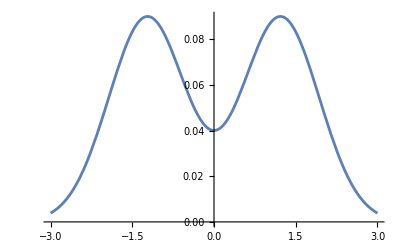

```mathematica
Plot[ff0[0,0,vz],{vz,-3,3}]
```

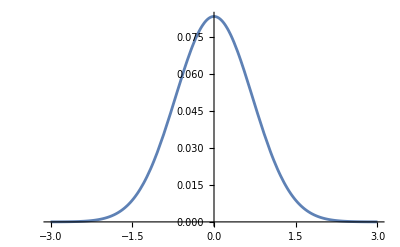

```mathematica
Plot[ff0[0,vz,1.5],{vz,-3,3}]
```

```mathematica
Integrate[ ( 1/3 (vx^2+vy^2+vz^2))ff0[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

1

```mathematica
Integrate[ {vx,vy,vz}ff0[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

{0,0,0}

## Get projection Rules ∫ Psi[v] f[v] ⅆv "Run Section"

```mathematica
getProjectionCoeff[a_,b_,c_]:=If[EvenQ[a] && EvenQ[b] && EvenQ[c],(2^(1/2+a/2+1/2 (5+b+c)) 3^(1/2+a/2+1/2 (-7+b+c)) 13^(-1/2-a/2+1/2 (1-b-c)) (2) (2) Gamma[(3+a)/2] Gamma[(1+b)/2] Gamma[(11+c)/2] (2))/(35 (1+a) π^(3/2)),0]
```

```mathematica
getProjectionWeight[a_,n_,l_]:=If[EvenQ[n],ψFactor[n,l]Total[CoefficientRules[ψProjA[vx,vy,vz,n,l,a],{vx,vy,vz}]/. Rule[{aa_,bb_,cc_},factor_] :>  factor getProjectionCoeff[aa,bb,cc]]/Sqrt[NormψA[a,n]],0]
```

## Define generation of the text file for the intial f "Run Section"

#### Generate the text file for the intial f

```mathematica
(*Pick an initial f and extract the coefficients for Andreas Basis and recover the projected function from the coefficients*)
getCoeffsA[theory_] := Block[{combs, weights, a,n,l},
combs = generateIDXset[theory];
weights = ConstantArray[0,Length[combs]];
Do[
n = comb⟦1⟧;a = comb⟦2⟧;l = comb⟦3⟧;
weights⟦getIDX[n,a,l]+1⟧=getProjectionWeight[a,n,l];
,{comb,combs}];
weights
];

getCoeffsForFileA[theory_] := Block[{combs, weights, a,n,l},
combs = generateIDXset[theory];
weights = ConstantArray[0,Length[combs]];
Do[
n = comb⟦1⟧;a = comb⟦2⟧;l = comb⟦3⟧;
weights⟦getIDX[n,a,l]+1⟧={{n,a,l},getProjectionWeight[a,n,l]};
,{comb,combs}];
weights

];
getInputForFileFromCoeffsA[theory_,weights_] := Block[{combs, input, a,n,l},
combs = generateIDXset[theory];
input = ConstantArray[0,Length[combs]];
Do[
n = comb⟦1⟧;a = comb⟦2⟧;l = comb⟦3⟧;
input⟦getIDX[n,a,l]+1⟧={{n,a,l},weights⟦getIDX[n,a,l]+1⟧};
,{comb,combs}];
input

];
buildFfromCoeffsA[theory_,weights_,xx_,yy_,zz_,Cx_,Cy_,Cz_ ] := Block[{combs, a,n,l},
combs = generateIDXset[theory];
f[x_,y_,z_] :=Sum[weights⟦getIDX[comb⟦1⟧,comb⟦2⟧,comb⟦3⟧]+1⟧ψFactor[comb⟦1⟧,comb⟦3⟧] 1/(√((2 π)^3))√(1/NormψA[comb⟦2⟧,comb⟦1⟧])ψProjA[x,y,z,comb⟦1⟧,comb⟦3⟧,comb⟦2⟧],{comb,combs}];
Simplify[f[xx-Cx,yy-Cy,zz-Cz]Exp[-((xx-Cx)^2 + (yy-Cy)^2 +(zz-Cz)^2)/2]]

];
```

```mathematica
getMediumVelocity[f_] := Block[{cx,cy,cz, ff},
Clear[x,y,z];
cx =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ x f[x,y,z]ⅆxⅆyⅆz;
cy =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ y f[x,y,z]ⅆxⅆyⅆz;
cz =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ z f[x,y,z]ⅆxⅆyⅆz;
ff = ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ f[x,y,z]ⅆxⅆyⅆz;
{cx/ff,cy/ff,cz/ff}
]
getMediumVelocity2[f_, offsetx_, offsety_, offsetz_] := Block[{cx,cy,cz, ff},
Clear[x,y,z];
cx =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (x+offsetx) f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
cy =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (y +offsety) f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
cz =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (z+offsetz) f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
ff = ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
{cx/ff,cy/ff,cz/ff}
]
getMediumVelocity[f_, offsetx_, offsety_, offsetz_] := Block[{cx,cy,cz, ff},
Clear[x,y,z];
cx =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (x) f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
cy =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (y ) f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
cz =∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (z) f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
ff = ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ f[x+offsetx,y+offsety,z+offsetz]ⅆxⅆyⅆz;
{cx/ff+offsetx,cy/ff+offsety,cz/ff+offsetz}
]
```

```mathematica
generateIDXset[theory][[1118]]
```

Do::iterb: Iterator {amax,theory} does not have appropriate bounds.

Part::partw: Part 1118 of {} does not exist.

{}⟦1118⟧

## Generate the text file for the intial f "Run Section"

```mathematica
NotebookDirectory[]
```

/Users/amat/Documents/Privat/Uni/Semester5/ACoM/dergeraet/AnjaMathematica/

```mathematica
distname="PztimesgaussianTest"
```

PztimesgaussianTest

```mathematica
theory={2,1,1,0,0};
(*theory = {10};*)
generatefFile[theory,getCoeffsForFileA[theory],NotebookDirectory[] <> "finit"<>distname<>"_Full2" ]
```

0 1.
1 0
2 -0.4213250442
3 0
4 0
5 0
6 0
7 0
8 0
9 0
10 0
11 1.332346775
12 0
13 0
14 0
15 0
16 1.259991852
17 0
18 0
19 0
20 0
21 0
22 0
23 0
24 0
25 0
26 0
27 0
28 0
29 0
30 0.4157680784
31 0
32 0
33 0
34 0

```mathematica
theory={10,9,9,8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0};
(*theory = {10};*)
generatefFile[theory,getCoeffsForFileA[theory],NotebookDirectory[] <> "finit"<>distname<>"_Full10" ];
```

```mathematica
theory={3,3,3,3,3,3,3};
(*theory = {10};*)
generatefFile[theory,getCoeffsForFileA[theory],NotebookDirectory[] <> "finit"<>distname<>"_3333333" ];
```

```mathematica
theory={4,4,4,4,4,4,4,4,4};
(*theory = {10};*)
generatefFile[theory,getCoeffsForFileA[theory],NotebookDirectory[] <> "finit"<>distname<>"_444444444" ];
```

```mathematica
(*Alternative projection space, since all uneven n are 0 anyway:*)
theory={10,0,9,0,8,0,7,0,6,0,5,0,4,0,3,0,2,0,1,0,0};
(*theory = {10};*)
generatefFile[theory,getCoeffsForFileA[theory],NotebookDirectory[] <> "finit"<>distname<>"_OnlyEvenN10" ];
```

```mathematica
theoryStrings= {"5","6","7","8","9","10","5 4 4 3 3 2 2 1 1 0 0","5 5 4 4 3 3 2 2 1 1 0 0","6 5 5 4 4 3 3 2 2 1 1 0 0","6 6 5 5 4 4 3 3 2 2 1 1 0 0","7 6 6 5 5 4 4 3 3 2 2 1 1 0 0","7 7 6 6 5 5 4 4 3 3 2 2 1 1 0 0","8 7 7 6 6 5 5 4 4 3 3 2 2 1 1 0 0","8 8 7 7 6 6 5 5 4 4 3 3 2 2 1 1 0 0","9 8 8 7 7 6 6 5 5 4 4 3 3 2 2 1 1 0 0","9 9 8 8 7 7 6 6 5 5 4 4 3 3 2 2 1 1 0 0","10 9 9 8 8 7 7 6 6 5 5 4 4 3 3 2 2 1 1 0 0"};

Do[
theory=Flatten@ToExpression@StringSplit[theoryString," "];
Print[theory];

generatefFile[theory,getCoeffsForFileA[theory],NotebookDirectory[] <> "finit"<>distname<> StringDelete[theoryString," "] ];

,{theoryString,theoryStrings}];
```

{5}

{6}

{7}

{8}

{9}

{10}

{5,4,4,3,3,2,2,1,1,0,0}

{5,5,4,4,3,3,2,2,1,1,0,0}

{6,5,5,4,4,3,3,2,2,1,1,0,0}

{6,6,5,5,4,4,3,3,2,2,1,1,0,0}

{7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}

{7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}

{8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}

{8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}

{9,8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}

{9,9,8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}

{10,9,9,8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}

```mathematica
theoryStrings= {"5 -1 4 -1 3 -1 2 -1 1 -1 0","5 -1 4 -1 3 -1 2 -1 1 -1 0 -1","6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0","6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1","7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0","7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1","8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0","8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1","9 -1 8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0","9 -1 8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1","10 -1 9 -1 8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0"};

Do[
theory=Flatten@ToExpression@StringSplit[theoryString," "];
Print[theory];

generatefFile[theory,getCoeffsForFileA[theory],NotebookDirectory[] <> "finit"<>distname<> StringDelete[StringReplace[theoryString,"-1"->"n"],{" "}] ];

,{theoryString,theoryStrings}];
```

{5,-1,4,-1,3,-1,2,-1,1,-1,0}

{5,-1,4,-1,3,-1,2,-1,1,-1,0,-1}

{6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0}

{6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0,-1}

{7,-1,6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0}

{7,-1,6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0,-1}

{8,-1,7,-1,6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0}

{8,-1,7,-1,6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0,-1}

{9,-1,8,-1,7,-1,6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0}

{9,-1,8,-1,7,-1,6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0,-1}

{10,-1,9,-1,8,-1,7,-1,6,-1,5,-1,4,-1,3,-1,2,-1,1,-1,0}

```mathematica
StringDelete[StringReplace[theoryStrings,"-1"->"n"],{" "}]
```

{5n4n3n2n1n0,5n4n3n2n1n0n,6n5n4n3n2n1n0,6n5n4n3n2n1n0n,7n6n5n4n3n2n1n0,7n6n5n4n3n2n1n0n,8n7n6n5n4n3n2n1n0,8n7n6n5n4n3n2n1n0n,9n8n7n6n5n4n3n2n1n0,9n8n7n6n5n4n3n2n1n0n,10n9n8n7n6n5n4n3n2n1n0}

```mathematica
generateIDXset[{5,-1,4,-1,3,-1,2,-1,1,-1,0}]
```

{{0,0,0},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{2,0,-2},{2,0,-1},{2,0,0},{2,0,1},{2,0,2},{2,1,-2},{2,1,-1},{2,1,0},{2,1,1},{2,1,2},{2,2,-2},{2,2,-1},{2,2,0},{2,2,1},{2,2,2},{2,3,-2},{2,3,-1},{2,3,0},{2,3,1},{2,3,2},{2,4,-2},{2,4,-1},{2,4,0},{2,4,1},{2,4,2},{4,0,-4},{4,0,-3},{4,0,-2},{4,0,-1},{4,0,0},{4,0,1},{4,0,2},{4,0,3},{4,0,4},{4,1,-4},{4,1,-3},{4,1,-2},{4,1,-1},{4,1,0},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,2,-4},{4,2,-3},{4,2,-2},{4,2,-1},{4,2,0},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,3,-4},{4,3,-3},{4,3,-2},{4,3,-1},{4,3,0},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{6,0,-6},{6,0,-5},{6,0,-4},{6,0,-3},{6,0,-2},{6,0,-1},{6,0,0},{6,0,1},{6,0,2},{6,0,3},{6,0,4},{6,0,5},{6,0,6},{6,1,-6},{6,1,-5},{6,1,-4},{6,1,-3},{6,1,-2},{6,1,-1},{6,1,0},{6,1,1},{6,1,2},{6,1,3},{6,1,4},{6,1,5},{6,1,6},{6,2,-6},{6,2,-5},{6,2,-4},{6,2,-3},{6,2,-2},{6,2,-1},{6,2,0},{6,2,1},{6,2,2},{6,2,3},{6,2,4},{6,2,5},{6,2,6},{8,0,-8},{8,0,-7},{8,0,-6},{8,0,-5},{8,0,-4},{8,0,-3},{8,0,-2},{8,0,-1},{8,0,0},{8,0,1},{8,0,2},{8,0,3},{8,0,4},{8,0,5},{8,0,6},{8,0,7},{8,0,8},{8,1,-8},{8,1,-7},{8,1,-6},{8,1,-5},{8,1,-4},{8,1,-3},{8,1,-2},{8,1,-1},{8,1,0},{8,1,1},{8,1,2},{8,1,3},{8,1,4},{8,1,5},{8,1,6},{8,1,7},{8,1,8},{10,0,-10},{10,0,-9},{10,0,-8},{10,0,-7},{10,0,-6},{10,0,-5},{10,0,-4},{10,0,-3},{10,0,-2},{10,0,-1},{10,0,0},{10,0,1},{10,0,2},{10,0,3},{10,0,4},{10,0,5},{10,0,6},{10,0,7},{10,0,8},{10,0,9},{10,0,10}}

```mathematica
Do[
theory=Flatten@ToExpression@StringSplit[theoryString," "];
Print[theory];

weights=getCoeffsForFileA[theory];
Do[
If[weight[[2]] ≠0, Print[weight]]
,{weight,weights}]

,{theoryString,theoryStrings[[7;;17;;4]]}]
```

Part::take: Cannot take positions 7 through 17 in {5 -1 4 -1 3 -1 2 -1 1 -1 0,5 -1 4 -1 3 -1 2 -1 1 -1 0 -1,6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0,6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1,7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0,7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1,8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0,8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1,9 -1 8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0,9 -1 8 -1 7 -1 6 -1 5 -1 4 -1 3 -1 2 -1 1 -1 0 -1,«1»}.

Do::iterb: Iterator {theoryString,theoryStrings⟦7;;17;;4⟧} does not have appropriate bounds.

Do[theory=Flatten[ToExpression[StringSplit[theoryString, ]]];Print[theory];weights=getCoeffsForFileA[theory];Do[If[weight⟦2⟧≠0,Print[weight]],{weight,weights}],{theoryString,theoryStrings⟦7;;17;;4⟧}]

## Test projection accuracy "Run Section"

```mathematica
buildFfromCoeffsAnormalized[theory_,weights_,xx_,yy_,zz_] := Block[{combs, a,n,l},
combs = generateIDXset[theory];
f[x_,y_,z_] :=Sum[weights⟦getIDX[comb⟦1⟧,comb⟦2⟧,comb⟦3⟧]+1⟧ψFactor[comb⟦1⟧,comb⟦3⟧] 1/(√((2 π)^3))√(1/NormψA[comb⟦2⟧,comb⟦1⟧])ψProjA[x,y,z,comb⟦1⟧,comb⟦3⟧,comb⟦2⟧],{comb,combs}];
Simplify[f[xx,yy,zz]Exp[-((xx)^2 + (yy)^2 +(zz)^2)/2]]

];
```

```mathematica
buildFfromCoeffsAshifted[theory_,weights_,xx_,yy_,zz_,ρ0_, vmean_, kk_ ] := Block[{combs, a,n,l},
combs = generateIDXset[theory];
f[x_,y_,z_] :=Sum[weights⟦getIDX[comb⟦1⟧,comb⟦2⟧,comb⟦3⟧]+1⟧ψFactor[comb⟦1⟧,comb⟦3⟧] 1/(√((2 π)^3))√(1/NormψA[comb⟦2⟧,comb⟦1⟧])ψProjA[x,y,z,comb⟦1⟧,comb⟦3⟧,comb⟦2⟧],{comb,combs}];
{Cx,Cy,Cz}=vmean;
Simplify[ρ0 kk^(-3/2)f[kk^(-1/2)(xx-Cx),kk^(-1/2)(yy-Cy),kk^(-1/2)(zz-Cz)]Exp[-((kk^(-1/2) (xx-Cx))^2 + (kk^(-1/2)(yy-Cy))^2 +(kk^(-1/2)(zz-Cz))^2)/2]]

];
```

```mathematica
Clear[vx,vy,vz]
theory={2,1,1,0,0};
theory={3,3,3,3,3,3,3};
fapproxFull2[x_,y_,z_] = buildFfromCoeffsAshifted[theory,getCoeffsA[theory],x,y,z,ρ0, vmean, kk ];
```

```mathematica
fapproxFull2[x,y,z]
```

1/(379097578860 √2 π^(3/2))ⅇ^(1/2 (-x^2-y^2-z^2)) (-48789185445+244950 x^12+244950 y^12+1028345818500 z^2-36439146315 z^4-16989994990 z^6+948599150 z^8+10995648 z^10-783840 z^12+18 x^10 (-1733522+81650 y^2-204125 z^2)-18 y^10 (1733522+204125 z^2)-25 y^8 (-50643017-13306032 z^2+264546 z^4)+5 y^6 (-4048551938-2060177045 z^2+90861276 z^4+774042 z^6)+3 y^4 (41297998170+44567601710 z^2-2881482575 z^4-67719192 z^6+3625260 z^8)+y^2 (-211343482350-689069150055 z^2+47643808830 z^4+3871112075 z^6-282614112 z^8+3527280 z^10)+5 x^8 (253215085+734850 y^4+66530160 z^2-1322730 z^4-18 y^2 (1733522+204125 z^2))+5 x^6 (-4048551938+979800 y^6-2060177045 z^2+90861276 z^4+774042 z^6-36 y^4 (1733522+204125 z^2)-20 y^2 (-50643017-13306032 z^2+264546 z^4))+3 x^4 (41297998170+1224750 y^8+44567601710 z^2-2881482575 z^4-67719192 z^6+3625260 z^8-60 y^6 (1733522+204125 z^2)-50 y^4 (-50643017-13306032 z^2+264546 z^4)+5 y^2 (-4048551938-2060177045 z^2+90861276 z^4+774042 z^6))+x^2 (-211343482350+1469700 y^10-689069150055 z^2+47643808830 z^4+3871112075 z^6-282614112 z^8+3527280 z^10-90 y^8 (1733522+204125 z^2)-100 y^6 (-50643017-13306032 z^2+264546 z^4)+15 y^4 (-4048551938-2060177045 z^2+90861276 z^4+774042 z^6)+6 y^2 (41297998170+44567601710 z^2-2881482575 z^4-67719192 z^6+3625260 z^8)))

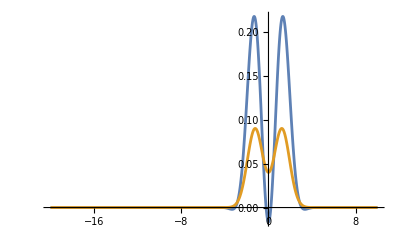

```mathematica
vvx=0;
vvy=0;
Plot[{fapproxFull2[vvx,vvy,cz],densitydist [vvx,vvy,cz]}, {cz,-20,10},PlotRange-> All]
```

```mathematica
g[cx_,cy_,cz_]=Simplify[densitydist [cx,cy,cz]-fapproxFull2[cx,cy,cz]]
```

-1/(379097578860 √2 π^(3/2))(-48789185445+244950 cx^12+244950 cy^12+1028345818500 cz^2-36439146315 cz^4-16989994990 cz^6+948599150 cz^8+10995648 cz^10-783840 cz^12+18 cx^10 (-1733522+81650 cy^2-204125 cz^2)-18 cy^10 (1733522+204125 cz^2)-25 cy^8 (-50643017-13306032 cz^2+264546 cz^4)+5 cy^6 (-4048551938-2060177045 cz^2+90861276 cz^4+774042 cz^6)+3 cy^4 (41297998170+44567601710 cz^2-2881482575 cz^4-67719192 cz^6+3625260 cz^8)+cy^2 (-211343482350-689069150055 cz^2+47643808830 cz^4+3871112075 cz^6-282614112 cz^8+3527280 cz^10)+5 cx^8 (253215085+734850 cy^4+66530160 cz^2-1322730 cz^4-18 cy^2 (1733522+204125 cz^2))+5 cx^6 (-4048551938+979800 cy^6-2060177045 cz^2+90861276 cz^4+774042 cz^6-36 cy^4 (1733522+204125 cz^2)-20 cy^2 (-50643017-13306032 cz^2+264546 cz^4))+3 cx^4 (41297998170+1224750 cy^8+44567601710 cz^2-2881482575 cz^4-67719192 cz^6+3625260 cz^8-60 cy^6 (1733522+204125 cz^2)-50 cy^4 (-50643017-13306032 cz^2+264546 cz^4)+5 cy^2 (-4048551938-2060177045 cz^2+90861276 cz^4+774042 cz^6))+cx^2 (-211343482350+1469700 cy^10-689069150055 cz^2+47643808830 cz^4+3871112075 cz^6-282614112 cz^8+3527280 cz^10-90 cy^8 (1733522+204125 cz^2)-100 cy^6 (-50643017-13306032 cz^2+264546 cz^4)+15 cy^4 (-4048551938-2060177045 cz^2+90861276 cz^4+774042 cz^6)+6 cy^2 (41297998170+44567601710 cz^2-2881482575 cz^4-67719192 cz^6+3625260 cz^8))) ⅇ^(1/2 (-cx^2-cy^2-cz^2))+(ⅇ^(-3/2-cx^2-cy^2-√6 cz-cz^2) (1+ⅇ^(2 √6 cz)))/(2 π^(3/2))

```mathematica
accum=0;
Do[
Do[
Do[
u=-10+ii*2/5;
v=-10+jj*2/5;
w=-10+kk*2/5;
accum+=N[g[u,v,w]*g[u,v,w]*8/125];
,{ii, 50}];
,{jj,50}];
,{kk,50}];
accum=Sqrt[accum];

accumf=0;
	Do[
	Do[
	Do[
	u=-10+ii*2/5;
	v=-10+jj*2/5;
	w=-10+kk*2/5;
	accumf+=N[densitydist[u,v,w]*densitydist[u,v,w]*8/125];
	,{ii,0, 50}];
	,{jj,0, 50}];
	,{kk,0, 50}];
	accumf=Sqrt[accumf];
accum/=accumf;
```

```mathematica
N[accum]
```

1.09007

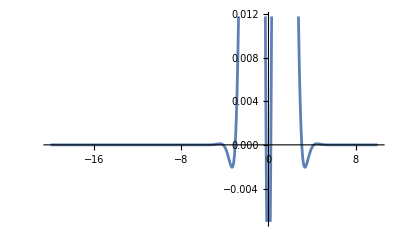

```mathematica
Plot[{fapproxFull2[0,0,cz]}, {cz,-20,10}]
```

```mathematica
Integrate[densitydist [cx,cy,cz],{cx,-∞,∞},{cy,-∞,∞},{cz,-∞,∞}]
```

1

```mathematica
ρ0
 vmean
 kk
```

1

{0,0,0}

1

```mathematica
theory={3,3,3,3,3,3,3};
fapproxFull2[x_,y_,z_] = buildFfromCoeffsAshifted[theory,getCoeffsA[theory],x,y,z,ρ0, vmean, kk ];
```

```mathematica
vmean
```

{0,0,0}

```mathematica
vvx=0;
man1=Manipulate[
Plot[{fapproxFull2[vvx,vvy,cz],densitydist [vvx,vvy,cz]}, {cz,-20,10},PlotRange-> All],{vvy,-10,0}]
```

```mathematica
N[ρ0 kk^(-3/2)]
```

1.

```mathematica
theory={3,3,3,3,3,3,3};
fapproxnormFull2[x_,y_,z_] = buildFfromCoeffsAnormalized[theory,getCoeffsA[theory] ,x,y,z];
```

```mathematica
vvx=0;
man2= Manipulate[
Plot[{fapproxnormFull2[vvx,vvy,cz],ff0 [vvx,vvy,cz]}, {cz,-10,10},PlotRange-> All],{vvy ,-5 kk^(-1/2),5 kk^(-1/2)}]
```